## Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalmu[μ_,T_,chem_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(chem/3)^2/T^2]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

## Plots

```mathematica
kfinal={0.47034270691413915,-0.25481763807967805};
kfinalu={0.8016955527941704,-0.36040626803845205};
kfinall={0.1389898610341079,-0.14922900812090412};
```

```mathematica
(*mDcalmu[μ_,T_,chem_,c_,d_]*)
mDcalmu[2π,0.5,0.1,kfinal[[1]],kfinal[[2]]]
```

0.975907

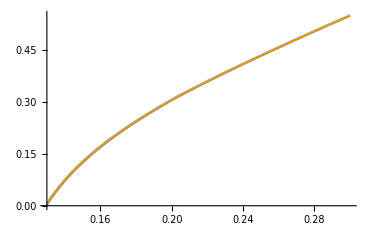

```mathematica
Plot[{mDcalmu[2π,T,0,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,T,0.155,kfinal[[1]],kfinal[[2]]]},{T,0.13,0.3}]
```

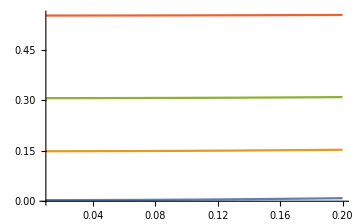

```mathematica
Plot[{mDcalmu[2π,0.13,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.155,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.2,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.3,x,kfinal[[1]],kfinal[[2]]]},{x,0.01,0.2}]
```

## Interpolation at Tc=155MeV

```mathematica
chemD=Table[{x,mDcalmu[2π,0.155,x,kfinal[[1]],kfinal[[2]]]},{x,0,0.3,0.01}]
```

{{0.,0.14846},{0.01,0.148472},{0.02,0.148505},{0.03,0.14856},{0.04,0.148638},{0.05,0.148738},{0.06,0.14886},{0.07,0.149005},{0.08,0.149171},{0.09,0.14936},{0.1,0.149571},{0.11,0.149804},{0.12,0.150058},{0.13,0.150335},{0.14,0.150634},{0.15,0.150955},{0.16,0.151297},{0.17,0.151662},{0.18,0.152048},{0.19,0.152456},{0.2,0.152886},{0.21,0.153337},{0.22,0.15381},{0.23,0.154304},{0.24,0.15482},{0.25,0.155357},{0.26,0.155916},{0.27,0.156495},{0.28,0.157096},{0.29,0.157718},{0.3,0.158361}}

```mathematica
tempmD=Table[{x,mDcalmu[2π,x,0,kfinal[[1]],kfinal[[2]]]},{x,0.155,0.158,0.00001}];
```

```mathematica
res=Range[Length[chemD]];
Do[res[[i]]=Position[tempmD[[All,2]],Nearest[tempmD[[All,2]],chemD[[i,2]]][[1]]][[1,1]],{i,1,Length[chemD]}]
```

```mathematica
mDdiff=Range[chemD];
Do[mDdiff[[i]]={chemD[[i,1]],chemD[[i,2]]-tempmD[[res[[i]],2]]},{i,Length[chemD]}];
```

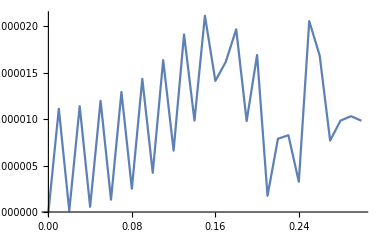

```mathematica
ListPlot[Abs[mDdiff],Joined->True]
```

```mathematica
bad={};
Do[If[Abs[mDdiff[[i,2]]]>1 10^-5,bad=Append[bad,{i}]],{i,Length[mDdiff]}]
```

```mathematica
bad
```

{{2},{4},{6},{8},{10},{12},{14},{16},{17},{18},{19},{21},{26},{27},{30}}

```mathematica
resnew=Delete[res,bad]
```

{1,2,5,10,17,26,37,50,92,112,123,134,146,185,199,228}

```mathematica
chemT=Delete[chemD[[All,1]],bad];
Do[chemT[[i]]=Append[{chemT[[i]]},tempmD[[resnew[[i]],1]]],{i,Length[resnew]}];
```

```mathematica
chemT
```

{{0.,0.155},{0.02,0.15501},{0.04,0.15504},{0.06,0.15509},{0.08,0.15516},{0.1,0.15525},{0.12,0.15536},{0.14,0.15549},{0.19,0.15591},{0.21,0.15611},{0.22,0.15622},{0.23,0.15633},{0.24,0.15645},{0.27,0.15684},{0.28,0.15698},{0.3,0.15727}}

```mathematica
chemT={{0.,0.155},{0.02,0.15501},{0.04,0.15504},{0.06,0.15509},{0.08,0.15516},{0.1,0.15525},{0.12,0.15536},{0.14,0.15549},{0.19,0.15591},{0.21,0.15611},{0.22,0.15622},{0.23,0.15633},{0.24,0.15645},{0.27,0.15684},{0.28,0.15698},{0.3,0.15727}};
```